```mathematica
good=Map[SetsToLabel[PointerToSets[#]]&,P[setp5]]
```

{1♁2♁3♁4♁5,12♁3♁4♁5,13♁2♁4♁5,14♁2♁3♁5,15♁2♁3♁4,1♁23♁4♁5,1♁24♁3♁5,1♁25♁3♁4,1♁2♁34♁5,1♁2♁35♁4,1♁2♁3♁45,123♁4♁5,124♁3♁5,125♁3♁4,12♁34♁5,12♁35♁4,12♁3♁45,134♁2♁5,135♁2♁4,13♁24♁5,13♁25♁4,13♁2♁45,145♁2♁3,14♁23♁5,14♁25♁3,14♁2♁35,15♁23♁4,15♁24♁3,15♁2♁34,1♁234♁5,1♁235♁4,1♁23♁45,1♁245♁3,1♁24♁35,1♁25♁34,1♁2♁345,1234♁5,1235♁4,123♁45,1245♁3,124♁35,125♁34,12♁345,1345♁2,134♁25,135♁24,13♁245,145♁23,14♁235,15♁234,1♁2345,12345}

```mathematica
bad=Table[SymbolToLabel[allGraphs5[k,"colofour"]],{k,Sort[allGraphs5AtomKeys,ComparePartition[SymbolToSets[allGraphs5[#1,"colofour"]],SymbolToSets[allGraphs5[#2,"colofour"]]]&]}]
```

{1♁2♁3♁4♁5,12♁3♁4♁5,13♁2♁4♁5,14♁2♁3♁5,15♁2♁3♁4,1♁23♁4♁5,1♁24♁3♁5,1♁25♁3♁4,1♁2♁34♁5,1♁2♁35♁4,1♁2♁3♁45,123♁4♁5,124♁3♁5,125♁3♁4,12♁34♁5,12♁35♁4,12♁3♁45,134♁2♁5,135♁2♁4,13♁24♁5,13♁25♁4,13♁2♁45,145♁2♁3,14♁23♁5,14♁25♁3,14♁2♁35,15♁23♁4,15♁24♁3,15♁2♁34,1♁234♁5,1♁235♁4,1♁23♁45,1♁245♁3,1♁24♁35,1♁25♁34,1♁2♁345,1234♁5,1235♁4,123♁45,1245♁3,124♁35,125♁34,12♁345,1345♁2,134♁25,135♁24,13♁245,145♁23,14♁235,15♁234,1♁2345,12345}

```mathematica
Table[StringJoin[Map[BlockVirtualValue[#,5]&, SymbolToSets[allGraphs5[k,"colofour"]]]],{k,Sort[allGraphs5AtomKeys,ComparePartition[SymbolToSets[allGraphs5[#1,"colofour"]],SymbolToSets[allGraphs5[#2,"colofour"]]]&]}]
```

{1666626666366664666656666,12666366664666656666,13666266664666656666,14666266663666656666,15666266663666646666,16666236664666656666,16666246663666656666,16666256663666646666,16666266663466656666,16666266663566646666,16666266663666645666,123664666656666,124663666656666,125663666646666,126663466656666,126663566646666,126663666645666,134662666656666,135662666646666,136662466656666,136662566646666,136662666645666,145662666636666,146662366656666,146662566636666,146662666635666,156662366646666,156662466636666,156662666634666,166662346656666,166662356646666,166662366645666,166662456636666,166662466635666,166662566634666,166662666634566,1234656666,1235646666,1236645666,1245636666,1246635666,1256634666,1266634566,1345626666,1346625666,1356624666,1366624566,1456623666,1466623566,1566623466,1666623456,12345}

```mathematica
Table[SymbolToLabel[allGraphs5[k,"colofour"]],{k,Sort[allGraphs5AtomKeys,ComparePartition[SymbolToSets[allGraphs5[#1,"colofour"]],SymbolToSets[allGraphs5[#2,"colofour"]]]&]}]
```

1♁2♁3♁4♁5 | 1♁23♁4♁5 | 1♁24♁3♁5 | 1♁2♁34♁5 | 1♁25♁3♁4 | 1♁2♁35♁4 | 1♁2♁3♁45
123♁4♁5 | 124♁3♁5 | 12♁34♁5 | 125♁3♁4 | 12♁35♁4 | 134♁2♁5 | 13♁24♁5
135♁2♁4 | 13♁25♁4 | 14♁23♁5 | 145♁2♁3 | 14♁25♁3 | 1♁234♁5 | 1♁235♁4
1♁23♁45 | 1♁245♁3 | 1♁24♁35 | 1♁25♁34 | 1♁2♁345 | 1234♁5 | 1235♁4
123♁45 | 1245♁3 | 124♁35 | 125♁34 | 12♁345 | 1345♁2 | 134♁25
135♁24 | 13♁245 | 145♁23 | 14♁235 | 15♁234 | 1♁2345 | 12♁3♁4♁5
13♁2♁4♁5 | 14♁2♁3♁5 | 15♁2♁3♁4 | 12♁3♁45 | 13♁2♁45 | 14♁2♁35 | 15♁23♁4
15♁24♁3 | 15♁2♁34 | 12345 |  |  |  |

```mathematica
Intersection[good,bad]//Length
```

52

```mathematica
Table[SymbolToSets[allGraphs5[k,"colofour"]],{k,Sort[allGraphs5AtomKeys,ComparePartition[SymbolToSets[allGraphs5[#1,"colofour"]],SymbolToSets[allGraphs5[#2,"colofour"]]]&]}]
```

{{{1},{2},{3},{4},{5}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2},{3},{4,5}},{{1,2,3},{4},{5}},{{1,2,4},{3},{5}},{{1,2,5},{3},{4}},{{1,2},{3,4},{5}},{{1,2},{3,5},{4}},{{1,3,4},{2},{5}},{{1,3,5},{2},{4}},{{1,3},{2,4},{5}},{{1,3},{2,5},{4}},{{1,4,5},{2},{3}},{{1,4},{2,3},{5}},{{1,4},{2,5},{3}},{{1},{2,3,4},{5}},{{1},{2,3,5},{4}},{{1},{2,3},{4,5}},{{1},{2,4,5},{3}},{{1},{2,4},{3,5}},{{1},{2,5},{3,4}},{{1},{2},{3,4,5}},{{1,2,3,4},{5}},{{1,2,3,5},{4}},{{1,2,3},{4,5}},{{1,2,4,5},{3}},{{1,2,4},{3,5}},{{1,2,5},{3,4}},{{1,2},{3,4,5}},{{1,3,4,5},{2}},{{1,3,4},{2,5}},{{1,3,5},{2,4}},{{1,3},{2,4,5}},{{1,4,5},{2,3}},{{1,4},{2,3,5}},{{1,5},{2,3,4}},{{1},{2,3,4,5}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}},{{1,2},{3},{4,5}},{{1,3},{2},{4,5}},{{1,4},{2},{3,5}},{{1,5},{2,3},{4}},{{1,5},{2,4},{3}},{{1,5},{2},{3,4}},{{1,2,3,4,5}}}

```mathematica
LongestCommonSubsequence[good,bad]//Length
```

52

```mathematica
BlockVirtualValue[block_,max_]:=Block[{result={}},
result=Join[block,Table[max+1,{k,Length[block]+1,max}]];
StringJoin[Map[ToString,result]]
];
```

```mathematica
BlockVirtualValue[{1,3,5},5]
```

13566

```mathematica
AlphabeticOrder["166666266666366666456666","156666266666366666466666"]
```

-1

```mathematica
ComparePartition[{{1},{2,3},{4},{5}},{{1,2},{3},{4},{5}}]
```

-1

```mathematica
ComparePartition[part1_,part2_]:=Block[{result,t1,t2,block1,block2,pos,size},
result=Sign[Length[part1]-Length[part2]];
If[result≠0,Goto[found]];

size=Max[Flatten[part1]];

t1=StringJoin[Map[BlockVirtualValue[#,size]&,part1]];
t2=StringJoin[Map[BlockVirtualValue[#,size]&,part2]];
result=Sign[AlphabeticOrder[t1,t2]];
If[result≠0,Goto[found]];


For[pos=1,pos≤Length[part1],pos++,
block1=part1[[pos]];
block2=part2[[pos]];
t1=BlockVirtualValue[block1,size];
t2=BlockVirtualValue[block2,size];
result=Sign[AlphabeticOrder[t1,t2]];
If[result≠0,Goto[found]];
];
result=0;

Label[found];
result
]
```

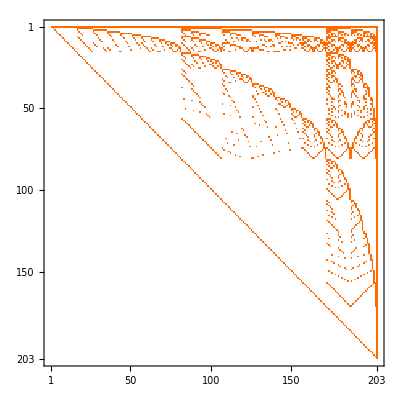

```mathematica
MobiusMatrix[allGraphs6]//Inverse//MatrixPlot
```

```mathematica
Table[ZetaP[var]//Flatten//Total,{var,{setp3,setp4,setp5,setp6,setp7}}]
```

{12,60,358,2471,19302}

```mathematica
Table[Sum[BellY[n,k,BellB[Range[n]]],{k,0,n}],{n,0,20}]
```

{1,1,3,12,60,358,2471,19302,167894,1606137,16733779,188378402,2276423485,29367807524,402577243425,5840190914957,89345001017415,1436904211547895,24227076487779802,427187837301557598,7859930038606521508}